# Par2 Par6 convectively triggered wave pinning for polarity establishment in C. elegans

Nate Debanjan Stephan

Jul 2008

## Initializations

### Functions

```mathematica
TwoErf[x_,c1_, c2_, m_]:= 1/2( Erf[m(x-c1)]-  Erf[m(x-c2)] );
```

### Parameters

Basic parameterset

```mathematica
vars = {ts-> 0.02, ton-> 1550,toff->2050,totP2->120, totP6->210,ins->2,tmax->20000, verbose->2, pssvb->2,  initialA2->A2startoff, initialA6->A6starton,xpos->30,Fa->-1, Fx->RealFlowx,Ft->Flowt, MinH->2};
```

```mathematica
rdvars={D2->0.15, D6->0.4,  koff2->0.0075, koff6 -> 0.0058,kon2->koff2, kon6 ->koff6*0.23,D2c->20000,D6c->20000, kc2->10, kc6 -> 0.27,start2->(kon2 totP2/L)/(koff2+kon2),start6->(kon6 totP6/L)/(koff6+kon6),α -> 2,β -> 1, L->120};
```

Note that throghout this document the embryo extends from {-20,20} in the spatial direction for the reflecting boundary model, and from {-60,60} for the preiodic boundary condition model.

### Flow field

No flow:

```mathematica
NoFlowx[x_]:=0;
```

Time evolution of the flowfield

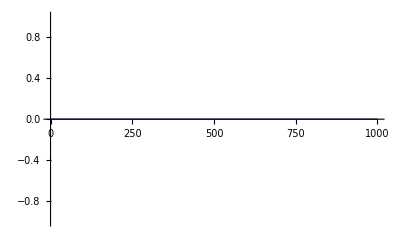

```mathematica
Flowt[t_]:=(Erf[ts (t - ton)]-Erf[ts (t - toff)])/2;
Plot[Evaluate[Flowt[t]/.vars],{t,0,1000},PlotRange->All,AxesLabel->{t}]
```

Total flowfield

```mathematica
Flow[x_,t_]:= Flowx[x] Flowt[t];
```

The exact shape of the flowfield near the end of the embryo at x=20 is not very well determined from an experimental point of view.

For periodic boundary conditions, we specify the following flow field:

```mathematica
FlowxPB[x_]:=-x/74 ⅇ^(-x^2/391) *(HeavisideTheta[x+59.99]-HeavisideTheta[x-59.99]);
```

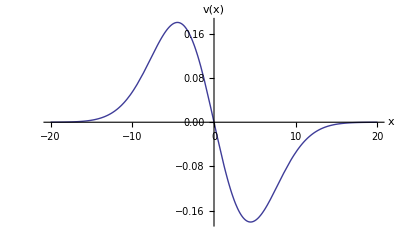

```mathematica
Plot[FlowxPB[x],{x,-60,60},AxesLabel->{x,v[x]}]
```

### Initial Par2/6 distributions

Initial P2 and P6 distributions, with half of the material at the cortex and half in the cytoplasm

```mathematica
mstart =0.5;
A2startseg[x_]:=start2 1/2(Erf[mstart(x+xpos)]-Erf[mstart(x-xpos)]);
A6startseg[x_]:=start6(1-1/2(Erf[mstart(x+xpos)]-Erf[mstart(x-xpos)]));
```

Homogeneous initial distributions, P2 all off.

```mathematica
A2startoff[x_]:=0;
A6startoff[x_]:=0;
A2starton[x_]:=start2;
A6starton[x_]:=start6;
```

## Convective RD Model

### Periodic boundary conditions

The solver

```mathematica
P26rdSolve[opts___]:= Module[{c=0,cm=1000,x,t,soln},
(*Numerical integration*)
If[Evaluate[verbose//.{opts}//.vars]>0,Print["Starting NDSolve..."];];

If[Evaluate[verbose//.{opts}//.vars]>2,Print["Options given: ",{opts}];];
soln=Monitor[NDSolve[Evaluate[{

D[A2[x,t], t]==D2 D[A2[x,t], x,x] - Fa Ft[t](Fx[x]D[A2[x,t], x]+A2[x,t]D[Fx[x], x])+kon2 B2[x,t]-koff2 A2[x,t] - kc2  A2[x,t]  A6[x,t]^α,
D[A6[x,t], t]==D6 D[A6[x,t], x,x] - Fa Ft[t](Fx[x]D[A6[x,t], x]+A6[x,t]D[Fx[x], x])+kon6 B6[x,t] -koff6 A6[x,t]-kc6  A6[x,t]  A2[x,t]^β,
D[B2[x,t], t]==D2c D[B2[x,t], x,x] -kon2 B2[x,t]  +koff2 A2[x,t] +  kc2  A2[x,t]  A6[x,t]^α,
D[B6[x,t], t]==D6c D[B6[x,t], x,x] - kon6 B6[x,t]+koff6 A6[x,t] +   kc6  A6[x,t]  A2[x,t]^β,

A2[x,0]==initialA2[x],
B2[x,0]==Evaluate[(totP2 - ∫_-60^60 A2[x,0]ⅆx)/L],
A6[x,0]==initialA6[x],
B6[x,0]==Evaluate[(totP6 - ∫_-60^60 A6[x,0]ⅆx)/L ],

A6[-60,t]==A6[60,t],
A2[-60,t]==A2[60,t],
B6[-60,t]==B6[60,t],
B2[-60,t]==B2[60,t]

}//.{opts}//.rdvars//.vars],{A2,A6,B2,B6},{x,-60,60},Evaluate[{t,0,tmax}/.{opts}/.rdvars/.vars],MaxStepFraction->1/100,EvaluationMonitor:>{c++;If[c>cm,c=0]}]⟦1⟧,ProgressIndicator[c,{0,cm}]];

If[Evaluate[verbose//.{opts}//.vars]>0,Print["Done."];];

If[Evaluate[verbose/.{opts}/.vars]>1,
Print["PAR-2c =  ",
NIntegrate[Evaluate[(B2[x,t])/.soln/.t->0],{x,-60,60}]," PAR-2m = ",NIntegrate[Evaluate[(A2[x,t])/.soln/.t->0],{x,-60,60}]];];

soln

];
```

Solve and Plot

```mathematica
P26rdPlot1[opts___]:= Module[{c=0,cm=1000,x,t,soln},

(* Plots output for single parameter set *)

soln=P26rdSolve[opts];

(*Plot graphs etc..*)

(*
BoundPosTable =  Sort[Table[Evaluate[{x,Abs[A2[x,t]-A6[x,t]]}/.soln/.t->toff//.{opts}//.rdvars//.vars],{x,-60,0,0.1}],#1[[2]]<#2[[2]]&];
BoundPos = BoundPosTable⟦1,1⟧;
DomFlow = Evaluate[{(∫_BoundPos^-BoundPos A2[x,t]ⅆx)/totP2}/.soln/.t->toff//.{opts}//.rdvars//.vars];


BoundPosTable =  Sort[Table[Evaluate[{x,Abs[A2[x,t]-A6[x,t]]}/.soln/.t->1//.{opts}//.rdvars//.vars],{x,-60,0,0.1}],#1[[2]]<#2[[2]]&];
BoundPos = BoundPosTable⟦1,1⟧;
DomStart = Evaluate[{(∫_BoundPos^-BoundPos A2[x,t]ⅆx)/totP2}/.soln/.t->1//.{opts}//.rdvars//.vars];
Print[DomStart, DomFlow]*)

(* Density plots *)
DensityPlot[Evaluate[A2[x,t]/.soln],{x,-60,60},Evaluate[{t,1,tmax}//.{opts}//.rdvars//.vars],PlotRange->{0,Automatic},FrameLabel->{"μm from Posterior Pole","Time(s)","P2"},PlotPoints->100,ImageSize->250]

DensityPlot[Evaluate[A6[x,t]/.soln],{x,-60,60},Evaluate[{t,1,tmax}//.{opts}//.rdvars//.vars],PlotRange->{0,Automatic},FrameLabel->{"μm from Posterior Pole","Time(s)","P6"},PlotPoints->100,ImageSize->250]




(* Start Distribution*)
Plot[Evaluate[{A2[x,t], A6[x,t]}/.soln/.t->1//.{opts}//.rdvars//.vars],{x,-60,0},PlotRange->{0,Automatic},AxesLabel->{"x","Before"},ImageSize->200]
(* Flow Distribution*)
Plot[Evaluate[{A2[x,t], A6[x,t]}/.soln/.t->toff//.{opts}//.rdvars//.vars],{x,-60,0},PlotRange->{0,Automatic},AxesLabel->{"x","Flow"},ImageSize->200]
(* Final Distribution*)
Plot[Evaluate[{A2[x,t]/1, A6[x,t]/1}/.soln/.t->tmax//.{opts}//.rdvars//.vars],{x,-60,0},PlotRange->{0,Automatic},AxesLabel->{"x","After"},ImageSize->200]


];

P26rdPlot2[opts___]:= Module[{c=0,cm=1000,x,t,soln},
(* Saves a Movie for a given simulation *)

soln=P26rdSolve[opts];
SetDirectory["/Users/goehring/movie"];
Do[
Export["a"<>ToString[PaddedForm[n,5]]<>".tif", 
Plot[{Evaluate[{A2[x,t]/0.6}/.soln/.t->n//.{opts}//.rdvars//.vars],Evaluate[{A6[x,t]/0.3}/.soln/.t->n//.{opts}//.rdvars//.vars](*,Evaluate[{5FlowxPB[x]},{x,-60,0}]*)},{x,-60,0},PlotRange->{0,1.3},(*Axes->False,Ticks->{{{0,"P"},{-60,"A"}},{0,1}},*)
Frame->True, FrameTicks->{{None,None},{{{0,"P"},{-60,"A"}},None}}, (*FrameLabel->{"Distance from Posterior Pole (μm)",ToString[n-250]<>" s"},*) FrameStyle-> {Black,Black,Black, Black}, PlotStyle->{{Green,Thickness[0.01]},{Red,Thickness[0.01]}(*,{Black, Dashed,Thin}*)}, ImageSize->300,BaseStyle->{FontFamily->"Helvetica",FontSize->24}],
"TIFF"],
{n,0,2000,10}]


];

P26rdPlot3[opts___]:= Module[{c=0,cm=1000,x,t,soln},
(* Saves Timecourse for a series of parameter changes *)
soln=P26rdSolve[opts];
data = Monitor[
Table[
Dist =  Sort[Table[Evaluate[{x,Abs[A2[x,t]-A6[x,t]]}/.soln/.t->n^2//.{opts}//.rdvars//.vars],{x,-60,0,0.5}],#1[[2]]<#2[[2]]&];
MinDif=Dist⟦1,2⟧;
MaxDif=Dist⟦120,2⟧;
Dist2 = Dist⟦1,1⟧;
Time = n^2;
{Time,Dist2,MinDif, MaxDif},{n,1,320,1}],n
];
If[Evaluate[run//.{opts}//.vars]==1,Export["P2_CytoShiftu_60.dat",data];];
If[Evaluate[run//.{opts}//.vars]==2,Export["P2_CytoShiftu_90.dat",data];];
If[Evaluate[run//.{opts}//.vars]==3,Export["P2_CytoShiftu_120.dat",data];];
If[Evaluate[run//.{opts}//.vars]==4,Export["P2_CytoShiftu_150.dat",data];];
If[Evaluate[run//.{opts}//.vars]==5,Export["P2_CytoShiftu_180.dat",data];];
];

P26rdPlot4[opts___]:= Module[{c=0,cm=1000,x,t,soln},
(* Saves a Timeseries for a given simulation *)
soln=P26rdSolve[opts];

data = Monitor[
Table[
A2Fit = FitTwoErf[ Table[Evaluate[{x,A2[x,t]}/.soln/.t->n//.{opts}//.rdvars//.vars],{x,-60,60,0.5}], opts];
A6Fit = FitTwoErf[ Table[Evaluate[{x,A6[x,t]}/.soln/.t->n//.{opts}//.rdvars//.vars],{x,-60,60,0.5}], opts];
B2out = Evaluate[B2[30,t]/.soln/.t->n//.{opts}//.rdvars//.vars];
B6out = Evaluate[B6[30,t]/.soln/.t->n//.{opts}//.rdvars//.vars];
Time = n-50;
{Time,B2out,B6out,A2Fit,A6Fit},{n,50,4000,10}],n
];

Export["P2_CytoShift.dat",data]

]
```

## Phase Space Sampler

Phase Space Sampler for the periodoc boundary condition case

```mathematica
PSSrd[xg_,yg_,opts___]:=Module[{c,cm,xi,ti, btime},
btime = AbsoluteTime[];

If[Evaluate[pssvb//.{opts}//.vars]>0,Print["Starting Phase Space Sampler..."];];

(* This is just for the progress indicator *)
c:=0; 
cm:= Length[xg⟦2⟧] * Length[yg⟦2⟧] ;

data=Monitor[
Table[
(* Progress *)
If[Evaluate[pssvb//.{opts}//.vars]>0,Print[xg⟦1⟧," = ",i,", ",yg⟦1⟧, " = ",j ,"; Calculation ", c+1, " of ", cm ];];

(*Numerical integration of current parameters*)
soln=P26rdSolve[Evaluate[xg⟦1⟧]-> i, Evaluate[yg⟦1⟧]->j, opts];
(*increment c*)
c=c+1;
(*Print Figures*)
If[Evaluate[pssvb//.{opts}//.vars]>3,Print[
DensityPlot[Evaluate[A2[x,t]/.soln],{x,-60,60},Evaluate[{t,0,tmax}//.{opts}//.rdvars//.vars],PlotRange->{0,Automatic},FrameLabel->{"x","t","A2"},PlotPoints->100,ImageSize->400]

DensityPlot[Evaluate[A6[x,t]/.soln],{x,-60,60},Evaluate[{t,0,tmax}//.{opts}//.rdvars//.vars],PlotRange->{0,Automatic},FrameLabel->{"x","t","A6"},PlotPoints->100,ImageSize->400]

(* Final Distribution*)
Plot[Evaluate[{A2[x,t], A6[x,t]}/.soln/.t->tmax//.{opts}//.rdvars//.vars],{x,-60,60},PlotRange->All,AxesLabel->{"x","A6 or A2"},ImageSize->400]
];];

(* error function fit*)

A2at0 = Evaluate[A2[0,ti]/.soln/.ti->tmax//.{opts}//.vars];
A2at60 = Evaluate[A2[60,ti]/.soln/.ti->tmax//.{opts}//.vars];
A6at0 = Evaluate[A6[0,ti]/.soln/.ti->tmax//.{opts}//.vars];
A6at60 = Evaluate[A6[60,ti]/.soln/.ti->tmax//.{opts}//.vars];

Domains = 1;
SlopeA2=0;
SlopeA6=0;
If[A2at60>A6at60&& A2at0>A6at0,BoundPos = 60; MagDif = A2at0/A6at0;SlopeA2 = 0;SlopeA6 = 0;Domains = 0;Print["PAR2 state"]];
If[A2at60< A6at60 && A2at0<A6at0, BoundPos = 0; MagDif = A6at0/A2at0;SlopeA2 = 0;SlopeA6 = 0;Domains = 0;Print["PAR6 state"]];
If[Domains==1,
BoundPosTable =  Sort[Table[Evaluate[{x,Abs[A2[x,t]-A6[x,t]]}/.soln/.t->tmax//.{opts}//.rdvars//.vars],{x,-60,0,0.1}],#1[[2]]<#2[[2]]&];
BoundPos = BoundPosTable⟦1,1⟧;
MagDif =(A2at0/A6at0+A6at60/A2at60)/2;
SlopeA2 = FitTwoErf[ Table[Evaluate[{x,A2[x,t]}/.soln/.t->tmax//.{opts}//.rdvars//.vars],{x,-60,60,0.5}], opts];

SlopeA6 = FitTwoErf[ Table[Evaluate[{x,A6[x,t]}/.soln/.t->tmax//.{opts}//.rdvars//.vars],{x,-60,60,0.5}], opts];
Print["Domains"]];


{i,j,BoundPos,MagDif,SlopeA2, SlopeA6 },
{i,xg⟦2⟧},{j,yg⟦2⟧}],ProgressIndicator[c,{0,cm}]];

(* the parameters at which the numerical integration was performed*)
xdata = Table[i,{i,xg⟦2⟧},{j,yg⟦2⟧}];
ydata = Table[j,{i,xg⟦2⟧},{j,yg⟦2⟧}];

(* the Par2 and Par6 result arrays, in a form that is compatible with ListContourPlot*)
dataout =  Flatten[MapThread[{#1⟦1⟧,#1⟦2⟧,#1⟦3⟧,#1⟦4⟧,#1⟦5⟧,#1⟦6⟧}&,{data},2],1];
R2Ldata = Flatten[MapThread[{#1, #2, #3⟦1⟧}&,{xdata, ydata, data},2],1];
R2Hdata = Flatten[MapThread[{#1, #2, #3⟦2⟧}&,{xdata, ydata, data},2],1];
R2Rdata = Flatten[MapThread[{#1, #2, #3⟦3⟧}&,{xdata, ydata, data},2],1];
R6Ldata = Flatten[MapThread[{#1, #2, #3⟦4⟧}&,{xdata, ydata, data},2],1];


If[Evaluate[pssvb//.{opts}//.vars]>0,Print["Done after ",Round[AbsoluteTime[] - btime],"s."];];

(**Display Results*)
SetDirectory["/Users/goehring/Desktop/simulations"];
If[Evaluate[run//.{opts}//.vars]==1,Export["P2sim_Run1.dat",dataout];];
];
```

This fits the double error functions to the result:

```mathematica
FitTwoErf[fitdata_,opts___]:= Module[{fitres, S1, S2, L, H, ret, a0, b0, Maxf, Minf, Maxx, Minx},
(*This is to seed FindFit with good initial values*)
Maxf =Max[(#⟦2⟧)&/@fitdata];
Minf =Min[(#⟦2⟧)&/@fitdata];

Maxx =fitdata⟦Ordering[(#⟦2⟧)&/@fitdata,-1],1⟧⟦1⟧;
Minx =fitdata⟦Ordering[(#⟦2⟧)&/@fitdata,1],1⟧⟦1⟧;

If[(Maxx > -20) && (Maxx < 20), a0 = Minf; b0 = Maxf-Minf;, a0 = Maxf; b0 = Minf-Maxf];

(*FindFit*)
fitres=FindFit[fitdata,a+b*TwoErf[x,c1,c2,m],{{a,a0},{b,b0},{c1,If[(Maxx-Minx)/2<0,(Maxx-Minx)/2+60,(Maxx-Minx)/2-60]},{c2,(Maxx-Minx)/2},{m,2}},x,MaxIterations->5000];

If[Evaluate[pssvb//.{opts}//.vars]>2,Print[Show[ListPlot[fitdata,PlotJoined->True,PlotStyle->{RGBColor[1,0,0]},PlotRange->All],Plot[Evaluate[a+b*TwoErf[x,c1,c2,m]/.fitres],{x,-40,40},PlotRange->All]]];];

(*Signs of the slopes at c1 and c2*)
S1 = Sign[m b /. fitres]; 
S2 = Sign[-m b /.fitres];

(*Length of the domain*)
L = If[S2<0, c2 - c1, c1 - c2]/.fitres;
L = If[L<0, L+120,L];

(*relative height of domain*)
H  =Abs[Maxf]/Abs[Minf];

If[Evaluate[pssvb//.{opts}//.vars]>1,Print["rel. Height and Length of domain: H = ", H, ", L = ", L];];

(* rel Height needs to be larger than 2 *)
If[H < Evaluate[MinH//.{opts}//.vars],ret=0;,ret=m /.fitres];

If[H < Evaluate[MinH//.{opts}//.vars],ret=0;,ret=L];

ret
];
```

## Solving the Model

### Periodic boundary conditions

Starting NDSolve...

Done.

PAR-2c =  90. PAR-2m = 30.

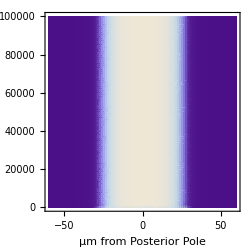
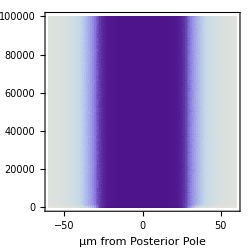
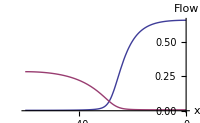
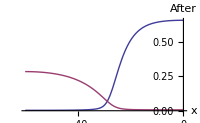
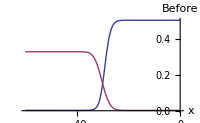

```mathematica
(* I USE THESE TO TEST SINGLE PARAMETER SETS *)

P26rdPlot1[tmax->100000,kc2->22.5, kc6->0.5,totP2->120, totP6->210,Dc2->200, Dc6->200,xpos->30,Fa->0, Fx-> FlowxPB,initialA2->A2startseg, initialA6->A6startseg,verbose->2, pssvb->0]
```

```mathematica
(* I USE THESE TO INTITIATE THE PARAMETER SPACE SEARCH *)

i =Table[j,{j,Join[Table[j,{j,0,1,0.01}],Table[j,{j,2.1,3.9,.1}],Table[j^2,{j,2,5,0.1}]]}];
j =Table[j,{j,Join[Table[j,{j^2,0,2,0.01}],Table[j,{j,2.1,3.9,.1}],Table[j^2,{j,2,5,0.1}]]}];

PSSrd[{kc2,i},{kc6,j},tmax->20000,Fa->0,Fx-> FlowxPB,initialA2->A2startseg, initialA6->A6startseg,verbose->0,run->1]
```

Starting Phase Space Sampler...

kc2 = 0., kc6 = 0.; Calculation 1 of 63001

$Aborted

```mathematica
(* I USE THESE TO INTITIATE THE PARAMETER SPACE SEARCH *)

i = Table[j,{j,0.1,0.5,0.01}];
j = Table[j^2,{j,1,10,0.1}];

PSSrd[{kc2,j},{kc6,i}, tmax->20000,Fa->0,Fx-> FlowxPB,initialA2->A2startseg, initialA6->A6startseg,verbose->0,run->1];
```

Starting Phase Space Sampler...

kc2 = 1., kc6 = 0.1; Calculation 1 of 3731

$Aborted

```mathematica
(* I USE THIS TO TEST A SERIES OF CHANGES *)

P26rdPlot3[tmax->150000,totP2->80 ,kc2->22.5, kc6->0.5,xpos->30,Fa->0, Fx-> FlowxPB,initialA2->A2startseg, initialA6->A6startseg,verbose->0, run->1]
P26rdPlot3[tmax->150000,totP2->100 ,kc2->22.5, kc6->0.5,xpos->30,Fa->0, Fx-> FlowxPB,initialA2->A2startseg, initialA6->A6startseg,verbose->0, run->2]
P26rdPlot3[tmax->150000,totP2->120,kc2->22.5, kc6->0.5,xpos->30,Fa->0, Fx-> FlowxPB,initialA2->A2startseg, initialA6->A6startseg,verbose->0, run->3]
P26rdPlot3[tmax->150000,totP2->140, kc2->22.5, kc6->0.5,xpos->30,Fa->0, Fx-> FlowxPB,initialA2->A2startseg, initialA6->A6startseg,verbose->0, run->4]
P26rdPlot3[tmax->150000,totP2->160, kc2->22.5, kc6->0.5,xpos->30,Fa->0, Fx-> FlowxPB,initialA2->A2startseg, initialA6->A6startseg,verbose->0, run->5]
```